Your Title Here

```mathematica
Manipulate[
Module[{g,y,z},
g=9.81;
y=pt[[1]];z=pt[[2]];

(*depth=If[#<0,0,#]&@(-ay/g*y+h-z);
P=ρ*g*depth;*)


Graphics[{

},ImageSize->{500,380},AspectRatio->Full]
],
Grid@{{
Control[{{ay,0,Row@{"acceleration (m/",Superscript["s",2],")"}},-5,5,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{ρ,1000,Row@{"density of fluid (kg/",Superscript["m",3],")"}},10,2000,10,Appearance->"Labeled",ImageSize->Small}],
Control[{{pt,{0,0}},{0,0},{1,5},Locator,Appearance->None}]
}}]
```

```mathematica
Manipulate[
Module[{d,hL,h},
d=0.5;hL=1;h=1.75;

Graphics[{
{Hue@0.5,Rectangle[{0,0},{d,hL}]},
Thick,Line[{{0,h},{0,0},{d,0},{d,h}}],
(*Arrow[{{1.05*d,h*#},{1.5*d,h*#}}]&/@Range[0.1,0.9,0.2]*)
If[ay>0,
Arrow[{{1.05*d,h*#},{1.05*d+d/4*Rescale[Abs@ay,{0,5}],h*#}}],
Arrow[{{-0.05*d,h*#},{-(0.05*d+d/4*Rescale[Abs@ay,{0,5}]),h*#}}]
]&/@Range[0.1,0.9,0.2]
},ImageSize->{500,380},AspectRatio->Full,PlotRange->{{-0.2,0.7},{0,h}}]
],
Control[{{ay,0,Row@{"acceleration (m/",Superscript["s",2],")"}},-5,5,0.1,Appearance->"Labeled"}]
]
```

```mathematica
N@1.75/#&/@Range@5
```

{1.75,0.875,0.583333,0.4375,0.35}

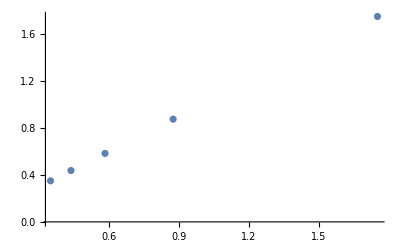

```mathematica
ListPlot[{1.75/#,1.75/#}&/@Range@5]
```

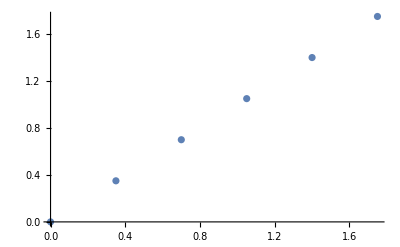





```mathematica
ListPlot[{1.75*#,1.75*#}&/@Range[0,1,0.2]]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX